Install MaTeX:

```mathematica
ResourceFunction["MaTeXInstall"][]
```

Check whether it works:

```mathematica
<<MaTeX`
```

```mathematica
MaTeX["\\sum_{k=1}^{\\infty} \\frac{1}{k^2} = \\frac{\\pi^2}{6}",FontSize->24]
```

-Graphics-

Put this code inside your init.m file (https://mathematica.stackexchange.com/questions/263698/how-to-write-latex-style-math-in-notebook-as-text/266146#266146). Modify if necessary.

```mathematica
SystemOpen["init.m"]
```

```mathematica
(*use MaTeX to format inline TeX*)
Needs["MaTeX`"];
$useMaTeXMag = 2;
$useMaTeXBaselineShift = 0;
$MaTeXPreamble = {};
InputAssistant`TeXStringToBoxes // Unprotect;
InputAssistant`TeXStringToBoxes[s_String] /; TrueQ[$useMaTeXQ] :=
	AdjustmentBox[
		ToBoxes @ MaTeX[s, Magnification -> $useMaTeXMag, "Preamble" -> $MaTeXPreamble],
		BoxBaselineShift -> $useMaTeXBaselineShift
	];
InputAssistant`TeXStringToBoxes // Protect;
$useMaTeXQ = True;
```

So that it would look something like this:

Now Ctrl+4 will return nice Graphics

-Graphics-

Instead of this ugly thing:

Add your preamble with necessary packages and other stuff:

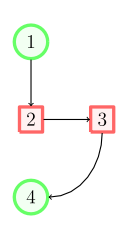

-Graphics-

```mathematica
$MaTeXPreamble={"\\usepackage{tikz}","\\usetikzlibrary{positioning}","\\usepackage{tikz-cd}","\\usetikzlibrary{cd}"};
```